# Slide Show Title: Additional Line for Title

## Slide Show Subtitle

Since then a number of studies have investigated the extratropical response to the tropical convection anomalies on the intraseasonal time scale, mostly focusing on the Northern Hemisphere (NH) large-scale circulation (Liebmann and Hartmann 1984; Weickmann et al. 1985; Lau and Phillips 1986; Knutson and Weickmann 1987; Ferranti et al. 1990; Hsu 1996; Matthews and Kiladis 1999; Matthews and Meredith 2004; Lin et al. 2009, 2010; Straus et al. 2015; Henderson et al. 2016; among many others).

It is only very recently that a number of studies started to examine the MJO influence on the midlatitude storm tracks and extratropical cyclones (Deng and Jiang 2011, hereafter DJ11; Lee and Lim 2012, hereafter LL12; Grise et al. 2013, hereafter Grise13; Takahashi and Shirooka 2014). Prior to these studies, Matthews and Kiladis (1999)

```mathematica
SetDirectory["/Users/lambda/Documents/Data/MJO"];
test=Import["OMI","Table"];
```

```mathematica
pc1=TimeSeries[test[[;;,5]],{{1979,1,1},Automatic,"Day"}];
pc2=TimeSeries[test[[;;,6]],{{1979,1,1},Automatic,"Day"}];
```

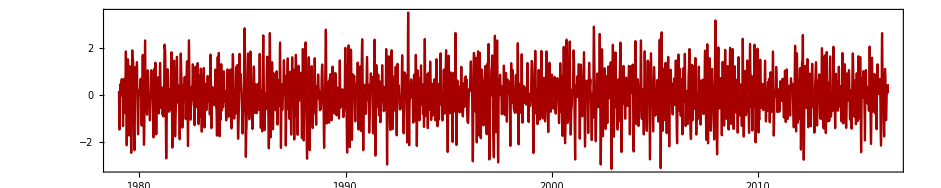

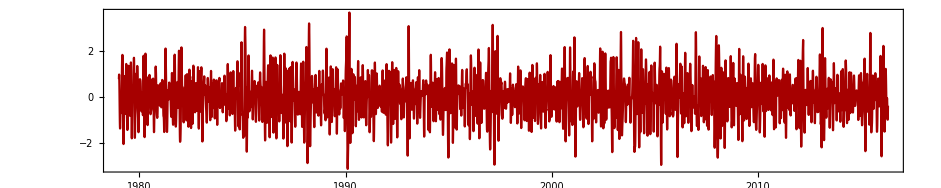

```mathematica
DateListPlot[pc1,AspectRatio->0.2]
DateListPlot[pc2,AspectRatio->0.2]
```

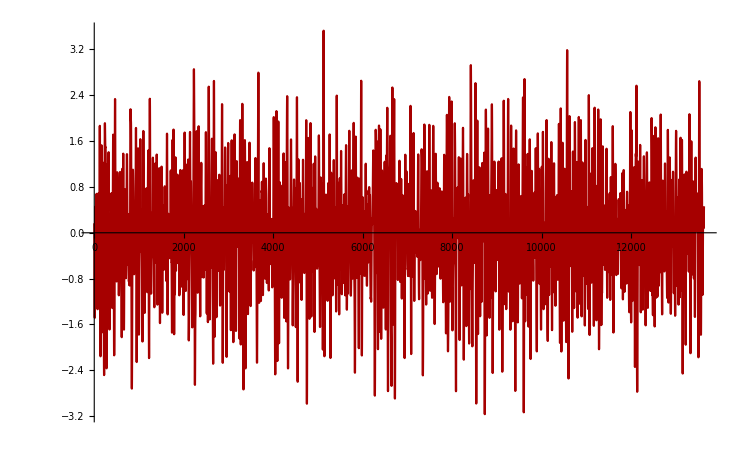

```mathematica
ListLinePlot[test[[;;,5]]]
```

```mathematica
TableForm[DFT[test[[;;,5]]][[1;;30]]*4]
```

227.183 | 0.821184 | 4.70174
203.448 | 0.767157 | -1.4648
147.762 | 0.718312 | 10.4717
187.368 | 0.666261 | -6.76672
146.177 | 0.630108 | 4.52209
244.502 | 0.583431 | 1.37885
232.017 | 0.582609 | 1.02332
177.026 | 0.56807 | -7.43459
169.329 | 0.566546 | 3.2853
173.643 | 0.556561 | -10.1234
176.453 | 0.553238 | -8.70779
164.229 | 0.547264 | 5.92676
212.984 | 0.54615 | -1.79687
301.238 | 0.538042 | -5.56721
207.316 | 0.532996 | 3.50023
234.009 | 0.529934 | -6.83406
189.319 | 0.517575 | 2.84683
263.401 | 0.515311 | -6.47715
365.933 | 0.5124 | 3.87198
141.254 | 0.507743 | 4.94087
181.747 | 0.506135 | -11.1122
149.381 | 0.504626 | 8.85959
172.544 | 0.495309 | -4.44325
191.312 | 0.483986 | 4.39404
258.408 | 0.483608 | 8.36017
193.348 | 0.483184 | 0.441702
237.061 | 0.478114 | 11.8445
178.183 | 0.477911 | 4.24317
198.993 | 0.476383 | -10.4933
119.57 | 0.475926 | -11.0533

```mathematica
DFT[data_, threshold_:0,sort_:1]:= 
 Module[{fs, s1, s = {}, i, mean, af, pf, pos, fr, frpos, fdata, fdatac, n, per,presult},
  n = Length[data];
  fs = Fourier[data];
  s1  = Drop[fs, -Floor[Length[fs]/2]];
  For[i = 2, i <= Length[s1], i++, 
   If[2/Sqrt[n] Abs[fs][[i]] > threshold, 
	 AppendTo[s, i]]];
  mean ={Infinity,Abs[fs[[1]]]/Sqrt[n],0};
  af = 2/Sqrt[n] Abs[fs][[s]];
  pf = Arg[fs][[s]];
  presult=Append[Transpose[{n/(s-1.0), af, pf}],mean];
  If[sort==1,Sort[presult,#1[[2]]>#2[[2]]&],presult]];
DFT::usage="DFT[data]={{T,Amp_max,Phase}...{T,Amp_min,Phase}}\ne.g. DFT[Cos[x]+y]={{∞,y,0},{2π,1,0}}";
DFTReconstruct[fp_,n_] := 
  Table[Sum[fp[[j, 2]] Cos[
        2 Pi / fp[[j, 1]] *t - fp[[j, 3]]], {j, 1, 
       Length[fp]}], {t, 0, n-1}];
DFTReconstruct::usage="DFTReconstruct[fp,n]=Reconstructed data(of length n) with frequencies listed in fp";
```

```mathematica
SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/SLP"];
file=FileNames["*.nc"];
```

```mathematica
lat = Import["slp.1948.nc", {"Datasets", "lat"}]
lon = Import["slp.1948.nc", {"Datasets", "lon"}]
```

```mathematica
Position[lat,30.]
Position[lat,70.]
Position[lon,220.]
Position[lon,245.]
```

{{25}}

{{9}}

{{89}}

{{99}}

```mathematica
data=Table[Block[{tempt=Import["slp."<>ToString[year]<>".nc",{"Datasets","slp"}]},
	Map[Flatten,tempt[[;;,9;;25,89;;99]]]],{year,1948,2017}];
```

```mathematica
Map[Dimensions[#]&,data]
```

{{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{1460,187},{1460,187},{1460,187},{1464,187},{760,187}}

```mathematica
Dimensions[Map[Flatten,test[[;;,9;;25,89;;99]]]]
```

{1460,187}

```mathematica
Length[data[[1]]]
```

1464

```mathematica
Dimensions[Flatten[data[[;;,;;,1]]],1]
```

{101572}

```mathematica
TableForm[DFT[Flatten[data[[;;,;;,1]]],1][[1;;100]]]
```

∞ | 101556. | 0
1472.06 | 266.465 | -0.472278
1451.03 | 239.21 | 2.50035
1430.59 | 126.21 | 2.73759
1493.71 | 102.727 | -0.497047
1410.72 | 74.1263 | 2.73506
457.532 | 66.5234 | 0.552552
459.602 | 65.2958 | 1.1751
615.588 | 63.9992 | -0.273479
608.216 | 62.5927 | 1.05711
6348.25 | 62.4064 | 0.229479
1336.47 | 60.0332 | 2.0482
546.086 | 58.8851 | 1.56287
243.578 | 57.6521 | 1.11996
244.752 | 57.3764 | -2.84017
1269.65 | 56.7808 | 2.19583
5078.6 | 56.0357 | -0.394442
94.0481 | 55.6166 | -0.0204191
396.766 | 54.3534 | 3.09321
453.446 | 54.3492 | 2.36559
659.558 | 53.2747 | 1.13465
195.331 | 52.7684 | -2.57333
98.5179 | 52.571 | 3.01803
564.289 | 52.5461 | 2.50469
295.267 | 52.2582 | 1.67025
225.215 | 51.4552 | -1.25105
117.424 | 51.4121 | 2.21544
1612.25 | 51.2271 | -0.122781
55.5646 | 50.6121 | -2.69035
209.427 | 50.5427 | -0.846676
705.361 | 50.4557 | 2.59706
102.702 | 50.1071 | -0.911887
2821.44 | 50.0598 | -1.78304
426.773 | 49.388 | -2.29386
70.1464 | 48.4108 | -0.942558
204.37 | 48.3528 | -2.13093
84.3621 | 48.13 | -1.15244
216.111 | 47.5005 | -0.227232
91.6715 | 47.4185 | 2.99384
190.567 | 47.4086 | -2.05391
93.4425 | 47.2908 | -2.43774
163.826 | 47.2511 | 2.71411
101.572 | 46.893 | -2.15906
231.9 | 46.7417 | -2.13203
77.0068 | 46.418 | 0.0522325
626.988 | 46.1235 | -1.80845
132.601 | 46.0594 | -2.08627
832.557 | 46.0538 | -1.36045
296.128 | 45.8212 | -2.12214
68.3526 | 45.7927 | -2.46431
81.1278 | 45.3876 | 2.49629
315.441 | 45.3103 | 3.07318
143.059 | 45.2697 | 2.69437
1209.19 | 45.1978 | -2.00817
638.818 | 45.0037 | 1.61251
2418.38 | 44.9302 | -0.391929
93.0999 | 44.9295 | 1.9798
130.555 | 44.8842 | 1.62376
44.0087 | 44.7531 | -1.00559
97.1981 | 44.4244 | 2.00888
883.235 | 44.3992 | 1.08905
76.1409 | 44.3969 | 2.64315
226.218 | 44.2604 | -0.340068
312.529 | 44.2216 | 0.932446
72.4996 | 43.894 | 0.222578
66.6046 | 43.8767 | 3.06176
1587.06 | 43.8606 | -0.381972
98.7094 | 43.779 | -0.902382
79.3531 | 43.7686 | 2.98623
16928.7 | 43.7595 | 0.157775
111.863 | 43.7256 | -1.70412
88.7867 | 43.6534 | -1.98409
86.2241 | 43.455 | 0.931192
124.323 | 43.4496 | 2.28687
868.137 | 43.2533 | 3.03648
131.061 | 43.166 | -0.366372
126.02 | 42.9409 | 0.381504
209.86 | 42.902 | 1.05389
50786. | 42.8479 | 1.51557
112.608 | 42.8021 | 2.4247
47.8887 | 42.7279 | -1.23417
103.224 | 42.7052 | -2.51156
344.312 | 42.6394 | -1.71141
65.785 | 42.4733 | -1.44241
101572. | 42.1348 | 2.12034
160.461 | 42.1166 | 0.202282
59.3988 | 42.115 | -0.892871
82.9159 | 42.0753 | -0.120411
485.99 | 42.0049 | 0.50609
114.641 | 41.9441 | 1.02449
1025.98 | 41.8313 | 2.48547
131.4 | 41.565 | 2.55431
570.629 | 41.545 | 1.89856
146.993 | 41.5328 | -1.69305
56.7125 | 41.4271 | -1.37522
540.277 | 41.4057 | 2.06002
76.0839 | 41.3531 | -1.67567
497.902 | 41.3327 | -0.586977
202.739 | 41.3095 | -3.09659
190.21 | 41.3063 | 2.275